## Solving TOV equations.

#### Equation of state:

Let’s try first just this one: relativistic case

```mathematica
pres[ϵ_]:=ϵ/3;
dener[p_]:=3p;
```

#### Constants

We need to declare the following constants

```mathematica
G = 6.673 10^-8;
Subscript[M, sol]=1.9891 10^33;
c = 2.99792458 10^10;
α=G Subscript[M, sol]/(10^5 c^2);
Subscript[E0, sol]= Subscript[M, sol] c^2;
km3 = (10.0^5)^3;
rmin = 0.001;
rmax = 350;
densup = 7.86;
```

The numerical values of the constants to non-dimensionalise the equations are:

```mathematica
beta[Pc_]:=4 Pi Pc km3 /Subscript[E0, sol];
β =beta[10^34];
```

```mathematica
{α,β}
```

{1.47685,0.000070293}

Now we can proceed to do the numerical integration

#### Newton Equations:

We solve first this simple case.

```mathematica
ListRG={};
Pc = 10^34;
Do[{ solution = NDSolve[{p'[r]== If[p[r]>0,(-α dener[p[r]*Pc] M[r])/(Pc r^2),0.0],
M'[r]==If[p[r]>0,(4 Pi (Pc km3)/Subscript[E0, sol]) r^2*dener[p[r] Pc]/Pc,0.0],p[rmin]==1,M[rmin]==0.0},{p,M},{r,rmin,x},MaxSteps->Infinity];
mass ad[x_]:=M[x]/.solution[[1]];
pressure ad[x_]:=p[x]/.solution[[1]];
If[pressure ad[x]<0,Break[],{capR=x}]
},{x,1.0,rmax,0.1}]
```

```mathematica
Table[Print[r,"\t", mass ad[r],"\t",pressure ad[r]*Pc,"\t", dener[pressure ad[r]*Pc]],{r,50,rmax,50}]
```

50	7.10847	7.04951×10^33	2.11485×10^34

100	35.6711	3.35334×10^33	1.006×10^34

150	72.6851	1.5662×10^33	4.69859×10^33

200	108.494	8.11011×10^32	2.43303×10^33

250	141.003	4.68576×10^32	1.40573×10^33

300	170.451	2.96394×10^32	8.89182×10^32

350	197.465	2.01274×10^32	6.03821×10^32

```mathematica
radius=capR
rstep=0.001;
dener[pressure ad[radius]*Pc]
```

350.

6.03821×10^32

```mathematica
c^2densup
```

7.06422×10^21

```mathematica
While[dener[pressure ad[radius]]≥densup,
radius=radius+rstep;
Print[radius,"\t",dener[pressure ad[radius]]]]
```

```mathematica
radius=radius-rstep;
ListRG=Append[ListRG,{Pc, radius, mass ad[radius]}];
Print[ListRG]
```

{{10000000000000000000000000000000000,233.332,130.535}}

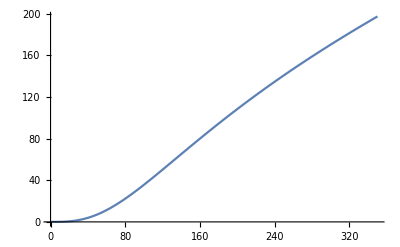

```mathematica
Plot[mass ad[x],{x,0,rmax}]
```

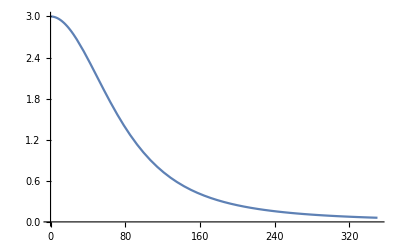

```mathematica
Plot[dener[pressure ad[x]],{x,0,rmax}]
```